Weston Slayton and Henry Cramer

```mathematica
Manipulate[
ParametricPlot[
{
(a+b)Cos[x]-b Cos[(a+b)x/b],
(a+b)Sin[x]-b Sin[(a+b)x/b]
},
{x,0,t},
PlotRange-> 2 b+a+1,
PlotPoints->100,
PlotStyle->Black,
Axes->False,
Prolog->{
EdgeForm[{Black,Thin}],LightBlue,Disk[{0,0},a],
LightPink,Disk[{(a+b)Cos[t],(a+b)Sin[t]},b],
Black,PointSize@0.02,Point[{(a+b)Cos[t]-b Cos[(a+b)t/b],(a+b)Sin[t]-b Sin[(a+b)t/b]}]
}
],
{{a,11},2,12,1,Appearance->"Labeled"},
{{b,6},1,a-1,1,Appearance->"Labeled"},
{{t,37},0.0001,2 b Pi/GCD[a,b],Appearance->"Labeled"}
]
```

```mathematica
Manipulate[
ParametricPlot[
{
(a-b)Cos[x]+b Cos[(a-b)x/b],
(a-b)Sin[x]-b Sin[(a-b)x/b]
},
{x,0,t},
PlotRange-> a+1,
PlotPoints->100,
PlotStyle->Black,
Axes->False,
Prolog->{
EdgeForm[{Black,Thin}],LightYellow,Disk[{0,0},a],
LightPurple,Disk[{(a-b)Cos[t],(a-b)Sin[t]},b],
Black,PointSize@0.02,Point[{(a-b)Cos[t]+b Cos[(a-b)t/b],(a-b)Sin[t]-b Sin[(a-b)t/b]}]
}
],
{{a,11},2,12,1,Appearance->"Labeled"},
{{b,3},1,a-1,1,Appearance->"Labeled"},
{{t,17},0.0001,2 b Pi/GCD[a,b],Appearance->"Labeled"}
]
```

```mathematica
hyperbola[{h_,k_},{a_,b_}]:=
ParametricPlot[
{
a Sec[x]+h,
b Tan[x]+k
},
{x,0,200},
PlotStyle->Red,
PlotRange->{
{h-Sqrt[(a^2+b^2)]-2,h+Sqrt[(a^2+b^2)]+2},
{k-b-6,k+b+6}
},
Epilog->{ 
PointSize@0.02,
Point[{#,k}]&/@{h,h-a,h+a,h-Sqrt[(a^2+b^2)],h+Sqrt[(a^2+b^2)]},
Opacity[0],EdgeForm[{Dashed}],Rectangle[{h-a,k-b},{h+a,k+b}],
Opacity[1],Dashed,InfiniteLine[{{h-a,k-b},{h+a,k+b}}],InfiniteLine[{{h-a,k+b},{h+a,k-b}}]
}
]
```

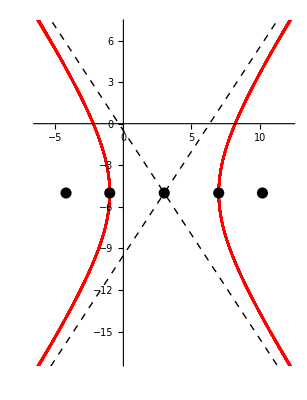

```mathematica
hyperbola[{3,-5},{4,6}]
```